```mathematica
SetDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0datan=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReVs[r_,mD_,σ_,rsb_]:=(σ (-2+ⅇ^(-mD (r+rsb)) (-2+4 ⅇ^(mD rsb)-mD rsb)+mD rsb Cosh[mD Abs[r-rsb]]+(2-2 Cosh[mD (r-rsb)]-mD rsb Sinh[mD (r-rsb)])/Sign[r-rsb]+(2 (r-rsb) Sinh[mD Abs[r-rsb]])/Abs[r-rsb]))/(2 mD^2 r)+σ rsb;
```

```mathematica
ReV[r_,mD_,α_,σ_,c_,rsb_]:=c-α mD-α Exp[-mD r]/r+(σ (-2+ⅇ^(-mD (r+rsb)) (-2+4 ⅇ^(mD rsb)-mD rsb)+mD rsb Cosh[mD Abs[r-rsb]]+(2-2 Cosh[mD (r-rsb)]-mD rsb Sinh[mD (r-rsb)])/Sign[r-rsb]+(2 (r-rsb) Sinh[mD Abs[r-rsb]])/Abs[r-rsb]))/(2 mD^2 r)+σ rsb-ReVs[10^-10,mD,σ,rsb];
```

```mathematica
Assuming[r>rsb,Limit[ReV[r,m,α,σ,c,rsb],m->0]]//Simplify
```

-α/r+rsb σ

```mathematica
Assuming[r<rsb,Limit[ReV[r,m,α,σ,c,rsb],m->0]]//Simplify
```

-α/r+r σ

```mathematica
ReVm0[r_,α_,σ_,c_]:=Piecewise[{{c-α/r+σ r,r<rsb},{c-α/r+σ rsb,r≥rsb}}]
```

```mathematica
rsb=1.5/0.197;
```

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0datan[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

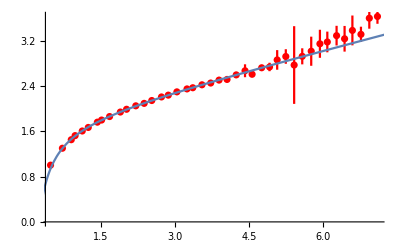

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

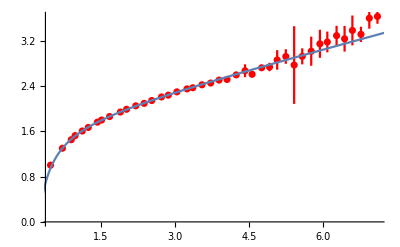

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

#### Use this one!

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,100},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal69r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal69r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal69r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

{21.8981,Null}

{0.469611,0.0468471}

{0.217455,0.0158241}

{1.77916,0.0590502}

```mathematica
αfinal69r={0.470941465156111,0.046943044902548435};(*1k run*)
σfinal69r={0.21707925160856373,0.015887095060722965};
cfinal69r={1.7807025997891905,0.05922159800246549};
```

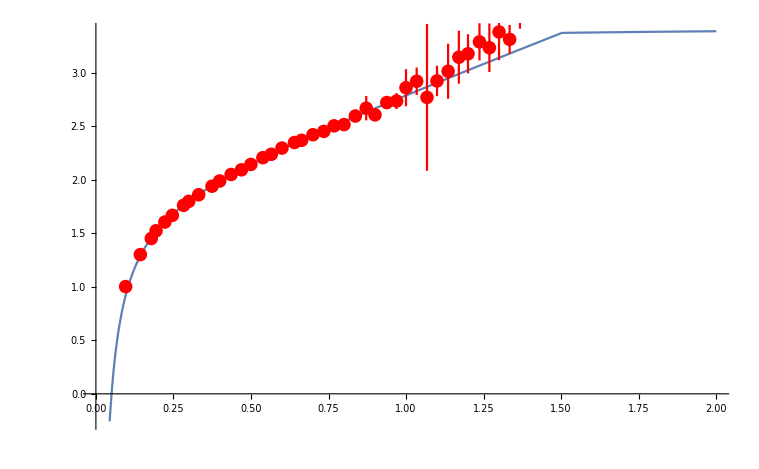

```mathematica
Show[{Plot[ReVm0[r/0.197327,αfinal69r[[1]],σfinal69r[[1]],cfinal69r[[1]]],{r,0,2}],ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All]}]
```

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

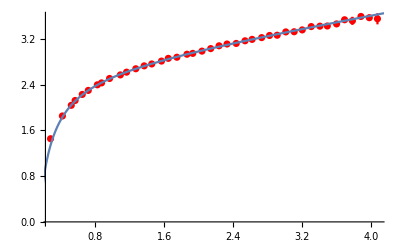

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

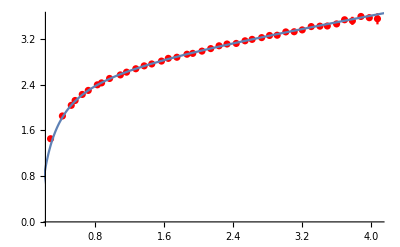

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

#### Use this one!

```mathematica
ParallelSow[exp_,tag_]:=Sow[exp,tag];
SetSharedFunction[ParallelSow];
res=Reap[Parallelize[Do[Block[{fit0,fit,al0,sig0,const0,al,sig,const},fit0=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r];
al0=al/.fit0["BestFitParameters"];
sig0=sig/.fit0["BestFitParameters"];
const0=const/.fit0["BestFitParameters"];fit=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{{al,al0},{sig,sig0},{const,const0}},r];
ParallelSow[al/.fit["BestFitParameters"],a];
ParallelSow[sig/.fit["BestFitParameters"],s];
ParallelSow[const/.fit["BestFitParameters"],c];],{ii,1,100},{i,1,Length[VaryFit]}]],{a,s,c}];//AbsoluteTiming
αfinal748r={Mean[res[[2,1,1]]],StandardDeviation[res[[2,1,1]]]}
σfinal748r={Mean[res[[2,2,1]]],StandardDeviation[res[[2,2,1]]]}
cfinal748r={Mean[res[[2,3,1]]],StandardDeviation[res[[2,3,1]]]}
Clear[res];
```

{19.1685,Null}

{0.384191,0.0270139}

{0.265103,0.0143863}

{2.64678,0.0421738}

```mathematica
αfinal748r={0.3844056964751124,0.026941644596478256};(*1k run*)
σfinal748r={0.2648012432461975,0.014468130850298858};
cfinal748r={2.6473195801293423,0.04219411293088157};
```

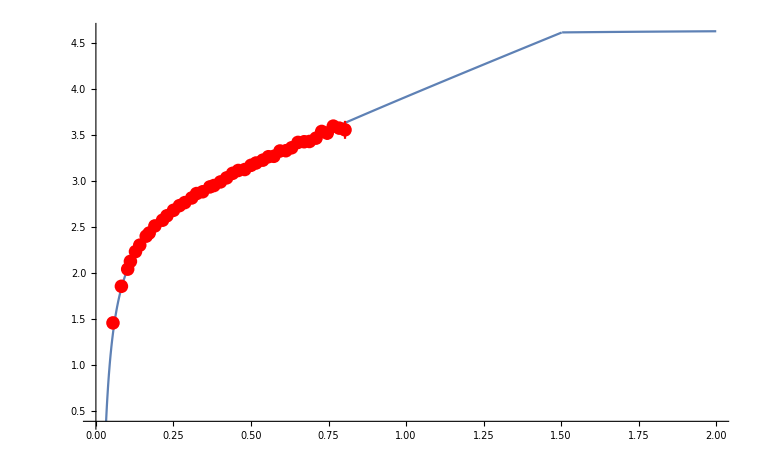

```mathematica
Show[{Plot[ReVm0[r/0.197327,αfinal748r[[1]],σfinal748r[[1]],cfinal748r[[1]]],{r,0,2}],ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All]}]
```

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
btinter1=Interpolation[Transpose[{T,β}],InterpolationOrder->1];
```

```mathematica
beta2T0res={αfinal69r,σfinal69r,cfinal69r};
beta7T0res={αfinal748r,σfinal748r,cfinal748r};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

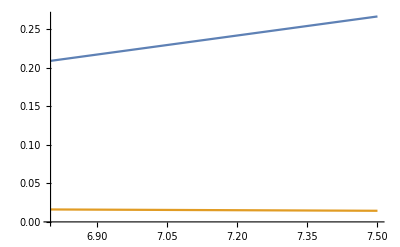

```mathematica
Plot[{T0constfit[[2]][x],T0errfit[[2]][x]},{x,6.8,7.5}]
```

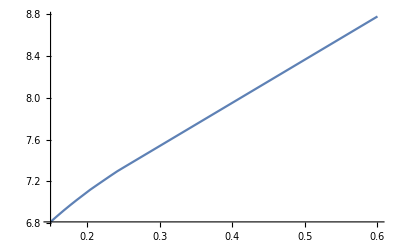

```mathematica
Plot[btinter1[x],{x,0.15,0.6}]
```

```mathematica
Table[T0constfit[[3]][β[[i]]],{i,1,Length[β]}]
```

{1.63129,1.7807,1.93012,2.11689,2.30366,2.37837,2.64732}

```mathematica
Table[T0errfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.0161317,0.0158871,0.0156424,0.0153366,0.0150308,0.0149085,0.0144681}

```mathematica
Tscanc=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
βTscanc=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
βTscanc1=Table[btinter1[i],{i,0.15,0.25,0.003}]
```

{6.81341,6.83171,6.85,6.86829,6.88659,6.90455,6.92159,6.93864,6.95568,6.97273,6.98977,7.00636,7.02225,7.03814,7.05403,7.06992,7.08581,7.10169,7.11758,7.1326,7.14686,7.16112,7.17538,7.18964,7.2039,7.21816,7.23241,7.24667,7.26065,7.27454,7.28843,7.30206,7.31445,7.32683}

```mathematica
βTscanb=Join[Table[btinter[i],{i,0.15,0.285,0.005}],Table[btinter1[i],{i,0.29,0.6,0.005}]]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81385,6.8448,6.87507,6.9047,6.93372,6.96216,6.99007,7.01759,7.04469,7.0713,7.0974,7.12298,7.1476,7.17171,7.19544,7.21888,7.24212,7.26541,7.28855,7.31137,7.33382,7.35585,7.3774,7.39842,7.41885,7.43864,7.45773,7.47607,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
βTscanb1=Table[btinter1[i],{i,0.15,0.6,0.005}]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81341,6.8439,6.87439,6.90455,6.93295,6.96136,6.98977,7.01695,7.04343,7.06992,7.0964,7.12288,7.14686,7.17063,7.19439,7.21816,7.24192,7.26528,7.28843,7.31032,7.33096,7.35161,7.37225,7.39289,7.41353,7.43417,7.45482,7.47546,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
Table[T0constfit[[2]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.209991,0.211526,0.21304,0.214534,0.216009,0.217466,0.218904,0.220325,0.221729,0.223118,0.224491,0.225852,0.227204,0.228541,0.229865,0.231173,0.232467,0.233745,0.235008,0.236243,0.237452,0.238646,0.239828,0.240999,0.242162,0.243316,0.244465,0.24561,0.246762,0.247909,0.249049,0.250179,0.251298,0.252407}

```mathematica
Table[T0constfit[[1]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.483796,0.481012,0.478266,0.475556,0.472881,0.47024,0.467632,0.465056,0.462509,0.459992,0.457502,0.455034,0.452583,0.450157,0.447757,0.445384,0.443038,0.44072,0.43843,0.436191,0.434,0.431834,0.42969,0.427566,0.425459,0.423365,0.421281,0.419205,0.417117,0.415036,0.41297,0.410921,0.408891,0.406881}

```mathematica
Table[T0constfit[[3]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{1.65197,1.67985,1.70735,1.73449,1.76128,1.78772,1.81384,1.83965,1.86515,1.89036,1.91529,1.94001,1.96456,1.98885,2.01288,2.03665,2.06014,2.08336,2.10629,2.12871,2.15066,2.17235,2.19381,2.21509,2.23619,2.25716,2.27803,2.29882,2.31973,2.34057,2.36126,2.38178,2.40211,2.42224}

```mathematica
Table[T0constfit[[2]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.209991,0.212538,0.215028,0.217466,0.219853,0.222194,0.224491,0.226755,0.228984,0.231173,0.233321,0.235426,0.237452,0.239435,0.241388,0.243316,0.245229,0.247145,0.249049,0.250926,0.252774,0.254586,0.256359,0.258089,0.25977,0.261398,0.262969,0.264478,0.266126,0.267824,0.269523,0.271221,0.27292,0.274618,0.276317,0.278015,0.279713,0.281412,0.28311,0.284809,0.286507,0.288206,0.289904,0.291602,0.293301,0.294999,0.296698,0.298396,0.300095,0.301793,0.303491,0.30519,0.306888,0.308587,0.310285,0.311984,0.313682,0.31538,0.317079,0.318777,0.320476,0.322174,0.323872,0.325571,0.327269,0.328968,0.330666,0.332365,0.334063,0.335761,0.33746,0.339158,0.340857,0.342555,0.344254,0.345952,0.34765,0.349349,0.351047,0.352746,0.354444,0.356143,0.357841,0.359539,0.361238,0.362936,0.364635,0.366333,0.368032,0.36973,0.371428}

```mathematica
Table[T0constfit[[1]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.483796,0.479177,0.474661,0.47024,0.465911,0.461667,0.457502,0.453397,0.449354,0.445384,0.44149,0.437673,0.434,0.430402,0.426862,0.423365,0.419897,0.416422,0.41297,0.409566,0.406216,0.402929,0.399714,0.396578,0.393529,0.390577,0.387728,0.384992,0.382003,0.378924,0.375844,0.372764,0.369684,0.366604,0.363525,0.360445,0.357365,0.354285,0.351205,0.348126,0.345046,0.341966,0.338886,0.335806,0.332727,0.329647,0.326567,0.323487,0.320407,0.317327,0.314248,0.311168,0.308088,0.305008,0.301928,0.298849,0.295769,0.292689,0.289609,0.286529,0.28345,0.28037,0.27729,0.27421,0.27113,0.268051,0.264971,0.261891,0.258811,0.255731,0.252651,0.249572,0.246492,0.243412,0.240332,0.237252,0.234173,0.231093,0.228013,0.224933,0.221853,0.218774,0.215694,0.212614,0.209534,0.206454,0.203375,0.200295,0.197215,0.194135,0.191055}

```mathematica
Table[T0constfit[[3]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{1.65197,1.69823,1.74346,1.78772,1.83108,1.87358,1.91529,1.9564,1.99689,2.03665,2.07565,2.11387,2.15066,2.18668,2.22214,2.25716,2.29189,2.32669,2.36126,2.39535,2.4289,2.46182,2.49402,2.52542,2.55595,2.58552,2.61405,2.64145,2.67138,2.70222,2.73306,2.76391,2.79475,2.82559,2.85643,2.88728,2.91812,2.94896,2.97981,3.01065,3.04149,3.07233,3.10318,3.13402,3.16486,3.19571,3.22655,3.25739,3.28824,3.31908,3.34992,3.38076,3.41161,3.44245,3.47329,3.50414,3.53498,3.56582,3.59666,3.62751,3.65835,3.68919,3.72004,3.75088,3.78172,3.81256,3.84341,3.87425,3.90509,3.93594,3.96678,3.99762,4.02846,4.05931,4.09015,4.12099,4.15184,4.18268,4.21352,4.24436,4.27521,4.30605,4.33689,4.36774,4.39858,4.42942,4.46027,4.49111,4.52195,4.55279,4.58364}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
mdfitrand[n_,runs_]:=Block[{res},res=Reap[ParallelDo[ParallelSow[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReV[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]],rsb],{{m,0.1}},r]["BestFitParameters"]],m],{ii,1,runs},{i,1,Length[VaryFit]}],m];
Return[{Mean[res[[2,1]]],StandardDeviation[res[[2,1]]]}]]
```

```mathematica
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
mdfitrandfinal[[1]]=mdfitrand[1,100]
```

{0.043091,0.10942}

```mathematica
mdfitrandfinal[[2]]=mdfitrand[2,100]
```

{0.145773,0.114498}

```mathematica
mdfitrandfinal[[3]]=mdfitrand[3,100]
```

{0.192347,0.120759}

```mathematica
mdfitrandfinal[[4]]=mdfitrand[4,100]
```

{0.284439,0.141289}

```mathematica
mdfitrandfinal[[5]]=mdfitrand[5,100]
```

{0.404048,0.120071}

```mathematica
mdfitrandfinal[[6]]=mdfitrand[6,100]
```

{0.412171,0.136168}

```mathematica
mdfitrandfinal[[7]]=mdfitrand[7,100]
```

{0.518623,0.156045}

```mathematica
mdfitrandfinal={{0.043091004301787576,0.1094201444760604},{0.14577289549172165,0.1144975437807689},{0.19234733898212233,0.12075947987531573},{0.28443869344344513,0.14128946474556042},{0.4040480113620337,0.12007124521152544},{0.4121709656595256,0.1361682974730346},{0.5186226216266835,0.15604540371766695}};
```

```mathematica
mdfitrandfinal={{0.06895350847644509,0.10221807625695377},{0.18664761415678735,0.13994985983632158},{0.2550574027173919,0.15018959554585246},{0.3718613325096623,0.1826759045545378},{0.5260504274058633,0.14840566777365682},{0.542139702256529,0.16900701712235927},{0.6672205262107764,0.1773092554997214}};(*1krun*)
```

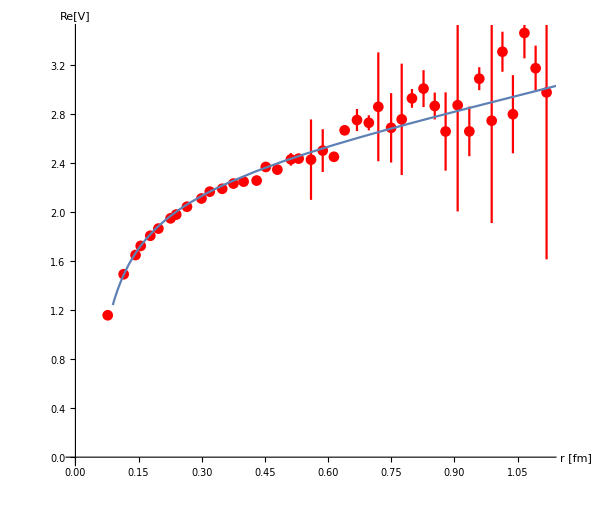

```mathematica
Block[{n=4},Show[ErrorListPlot[ReVdataTe[n],PlotStyle->Red,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}],Plot[ReV[r/0.197,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]],rsb],{r,0,3}]]]
```

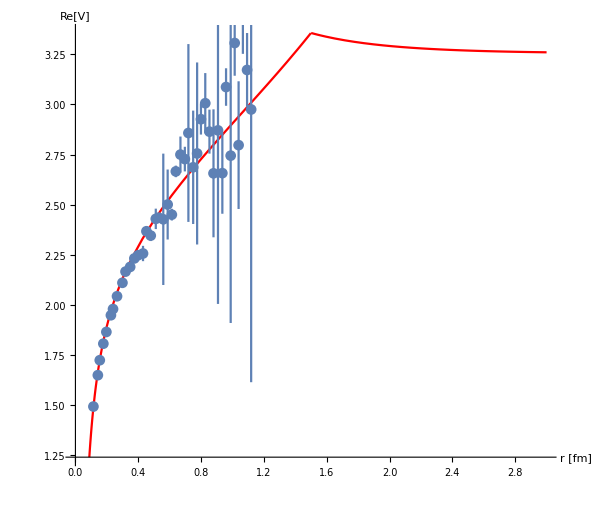

```mathematica
Block[{n=4},Show[Plot[ReV[r/0.197,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]],rsb],{r,0,3},PlotStyle->Red,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}],ErrorListPlot[ReVdataTe[n]]]]
```

## Plotting of imaginary part

```mathematica
Vsk[k_,rsb_,σ_]:=4π σ((-2+(2-k^2 rsb^2) Cos[k rsb]+2 k rsb Sin[k rsb])/k^4+rsb(k rsb Cos[k rsb]-Sin[k rsb])/k^3)
```

```mathematica
Imϵk[k_,mD_,T_]:=-π T(k mD^2)/((k^2+mD^2)^2);
```

```mathematica
(4π)/(2π)^3 k^2 Sinc[k r]Imϵk[k,mD,T]Vsk[k,rsb,σ]//FullSimplify
```

-(2 mD^2 T σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/(k (k^2+mD^2)^2)

```mathematica
ImVsI[r_,rsb_,mD_,α_,σ_,T_]:=Block[{norm=NIntegrate[(2 mD^2 T σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]))/(k (k^2+mD^2)^2),{k,0,∞}]},NIntegrate[(2 mD^2 T σ (-2+2 Cos[k rsb]+k rsb Sin[k rsb]) Sinc[k r])/(k (k^2+mD^2)^2),{k,0,∞}]-norm+T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])];
```

```mathematica
ImVc[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
```

```mathematica
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=(T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4]);
```

```mathematica
rsb=1.5/0.197;
```

```mathematica
ImVsb[r_,mD_,α_,σ_,T_]:=Piecewise[{{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],r<rsb},{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 (rsb)^2)/4])+1/4 mD √π (rsb)^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 (rsb)^2)/4],r≥rsb}}];
```

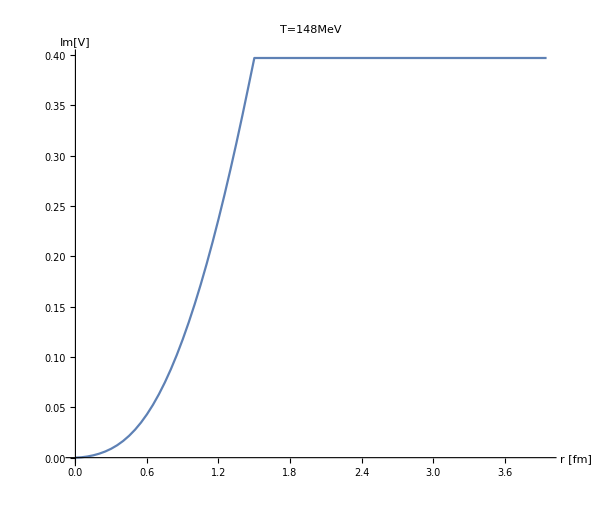

```mathematica
xsb=DiscretePlot[ImVsb[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

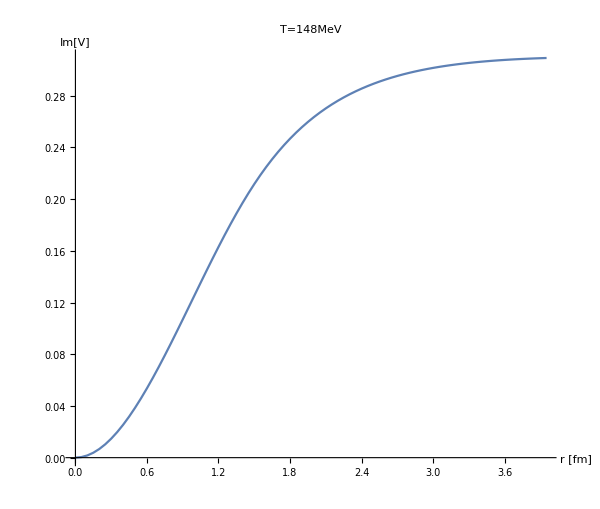

```mathematica
xI=DiscretePlot[ImVsI[r/0.197,rsb,mdfitrandfinal[[3,1]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

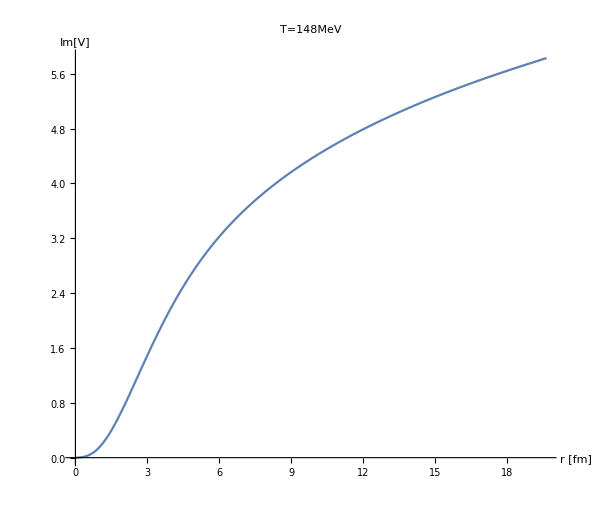

```mathematica
x=DiscretePlot[ImV[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,19.7,1/20},Filling->None,Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]
```

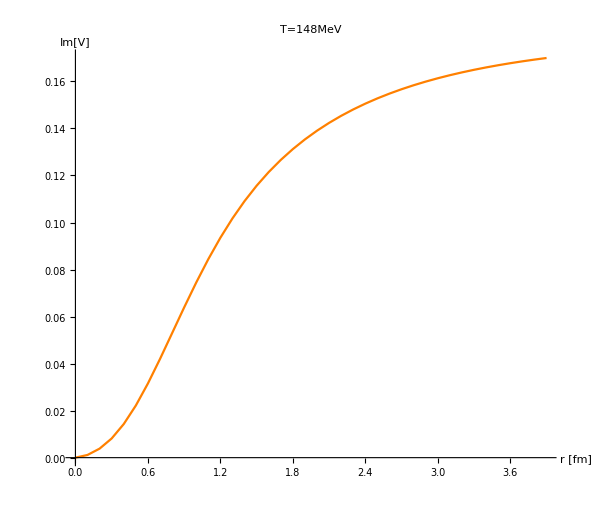

```mathematica
y=DiscretePlot[ImVold[r/0.197,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],0.148],{r,1/1000,4,1/10},Filling->None,Joined->True,PlotStyle->Orange,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=148MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600},PlotRange->All]
```

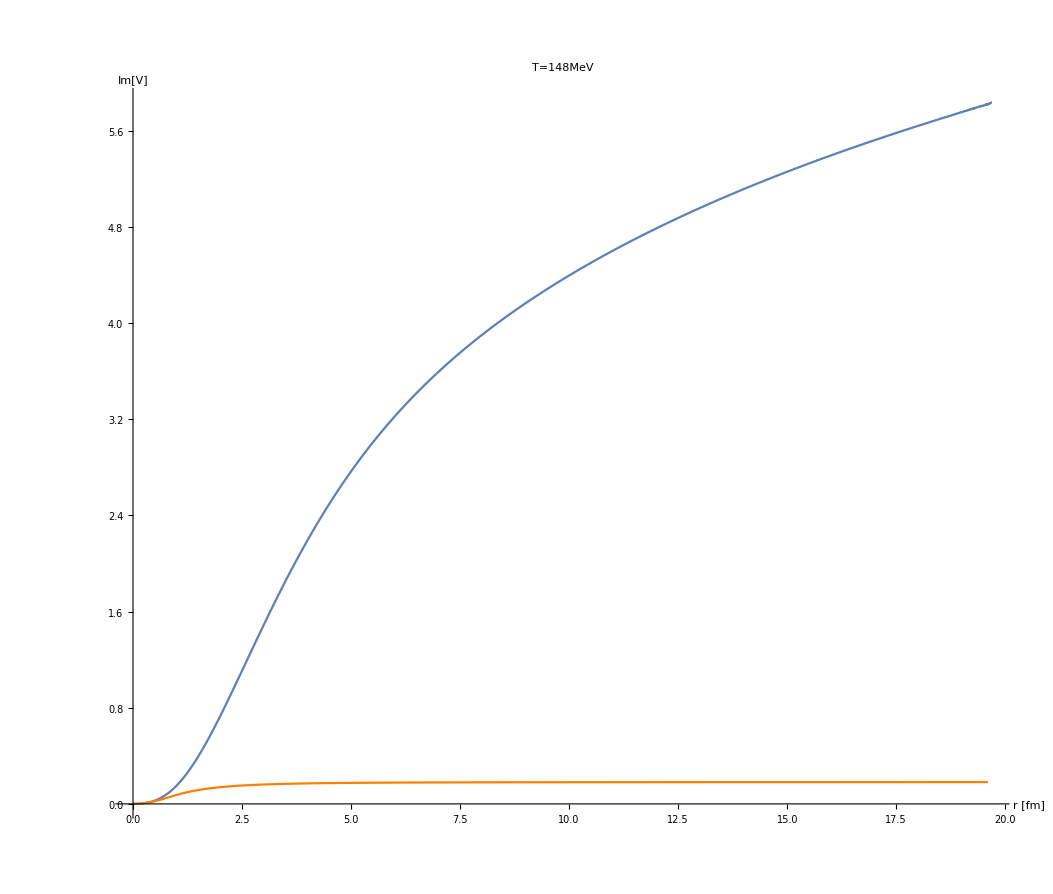

```mathematica
Show[x,y]
```

```mathematica
Show[xsb,y]
```

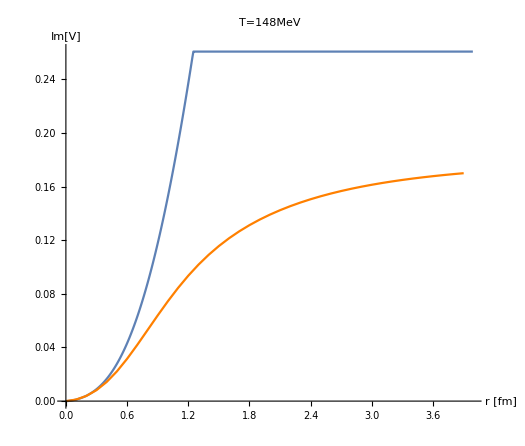

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVold[r_,mD_,α_,σ_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20]-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2 0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

## Combining into single figure

### Real Part

```mathematica
β1={6.9,7.48,6.8,6.9,7,7.125,7.25,7.3,7.48};
```

```mathematica
αcontβ1=Table[T0constfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.470941,0.384406,0.485861,0.470941,0.456022,0.437372,0.418722,0.411262,0.384406}

```mathematica
σcontβ1=Table[T0constfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.217079,0.264801,0.208851,0.217079,0.225307,0.235592,0.245877,0.249991,0.264801}

```mathematica
ccontβ1=Table[T0constfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{1.7807,2.64732,1.63129,1.7807,1.93012,2.11689,2.30366,2.37837,2.64732}

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
TempP={"T=0.24T_C","T=0.42T_C","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
TempP={"T≈0(β=6.9)","T≈0(β=7.48)","T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

```mathematica
For[l=1,l≤ 2,l++,PotReRescale[l]=T0data[[l]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,c}];
```

```mathematica
For[l=1,l≤ 5,l++,PotReRescale[l+2]=ReVdataTe[l]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45l+5.,c}];
```

```mathematica
For[l=6,l≤ 7,l++,PotReRescale[l+2]=ReVdataTe[l][[;;-14]]/.{a_,b_,c_}:>{a,b-ccontβ1[[l+2]]-0.45 l+5.,c}];
```

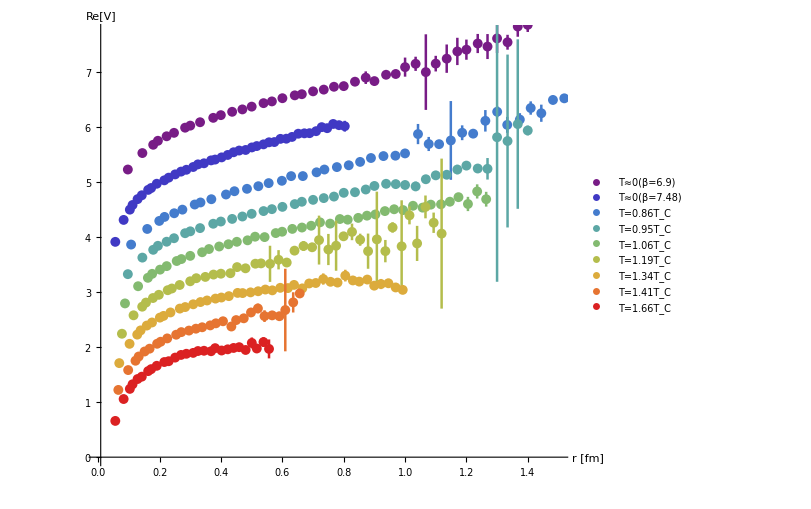

```mathematica
ReVdatPlot=ErrorListPlot[Table[PotReRescale[l],{l,1,9}],PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsolutePointSize[7.1],AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotLegends->Placed[PointLegend[TempP, LegendMarkerSize->8,LegendLayout->{"Row",3}],{0.66,0.12}],AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
ReVplot=Join[Table[ReVm0[r/0.197327,αcontβ1[[l]],σcontβ1[[l]],ccontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.,{l,1,2}],Table[ReV[r/0.197327,mdfitrandfinal[[l,1]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]],rsb]-ccontβ1[[l+2]]-0.45l+5.,{l,1,7}]];
```

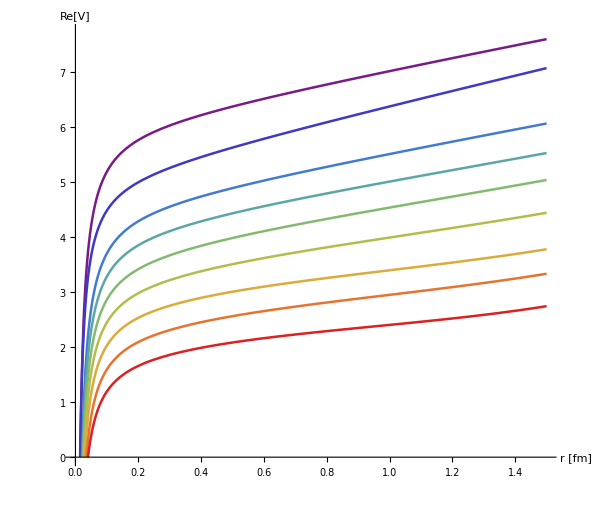

```mathematica
ReVanPlot=Plot[ReVplot,{r,0.001,1.5},PlotRange->{{0.00001,1.5},{0.,7.7}},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[0,1,1/8]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

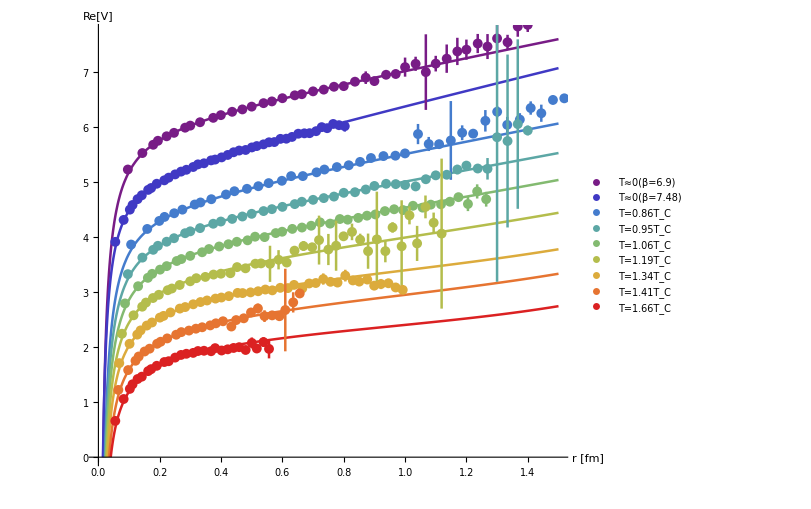

```mathematica
Show[{ReVanPlot,ReVdatPlot}]
```

```mathematica
αecontβ1=Table[T0errfit[[1]][β1[[i]]],{i,1,Length[β1]}]
```

{0.046943,0.0269416,0.0503916,0.046943,0.0434945,0.0391839,0.0348732,0.033149,0.0269416}

```mathematica
σecontβ1=Table[T0errfit[[2]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0158871,0.0144681,0.0161317,0.0158871,0.0156424,0.0153366,0.0150308,0.0149085,0.0144681}

```mathematica
cecontβ1=Table[T0errfit[[3]][β1[[i]]],{i,1,Length[β1]}]
```

{0.0592216,0.0421941,0.0621574,0.0592216,0.0562858,0.0526161,0.0489464,0.0474785,0.0421941}

```mathematica
ReVe[r_,l_,a_]:=ReV[r/0.197327,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],ccontβ1[[l+2]],rsb]-ccontβ1[[l+2]]-0.45l+5.;
```

```mathematica
ReV0e[r_,l_,a_]:=ReVm0[r/0.197327,αcontβ1[[l]]-a αecontβ1[[l]],σcontβ1[[l]]+a σecontβ1[[l]],ccontβ1[[l]]+a cecontβ1[[l]]]-ccontβ1[[l]]-0.45*If[l==1,0,l]+6.;
```

```mathematica
TempP={"T=41MeV","T=72MeV","T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

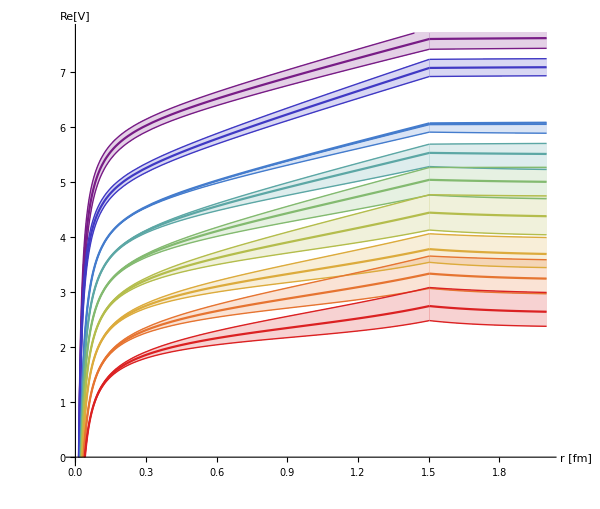

```mathematica
ReVanPlotError=Plot[{ReV0e[r,1,0],ReV0e[r,1,1],ReV0e[r,1,-1],ReV0e[r,2,0],ReV0e[r,2,1],ReV0e[r,2,-1],ReVe[r,1,0],ReVe[r,1,1],ReVe[r,1,-1],ReVe[r,2,0],ReVe[r,2,1],ReVe[r,2,-1],ReVe[r,3,0],ReVe[r,3,1],ReVe[r,3,-1],ReVe[r,4,0],ReVe[r,4,1],ReVe[r,4,-1],ReVe[r,5,0],ReVe[r,5,1],ReVe[r,5,-1],ReVe[r,6,0],ReVe[r,6,1],ReVe[r,6,-1],ReVe[r,7,0],ReVe[r,7,1],ReVe[r,7,-1]},{r,0.001,2},PlotRange->{{0.00001,2},{0.,7.7}},PlotStyle->{RGBColor[0.471412, 0.108766, 0.527016],{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},RGBColor[0.250728, 0.225386, 0.769152],{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},RGBColor[0.266122, 0.486664, 0.802529],{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},RGBColor[0.36048, 0.655759, 0.645692],{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},RGBColor[0.513417, 0.72992, 0.440682],{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},RGBColor[0.705038, 0.742591, 0.299167],{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},RGBColor[0.863512, 0.670771, 0.236564],{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},RGBColor[0.902853, 0.453964, 0.192014],{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},RGBColor[0.857359, 0.131106, 0.132128],{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600},PlotRange->{{0,1.5},All}]
```

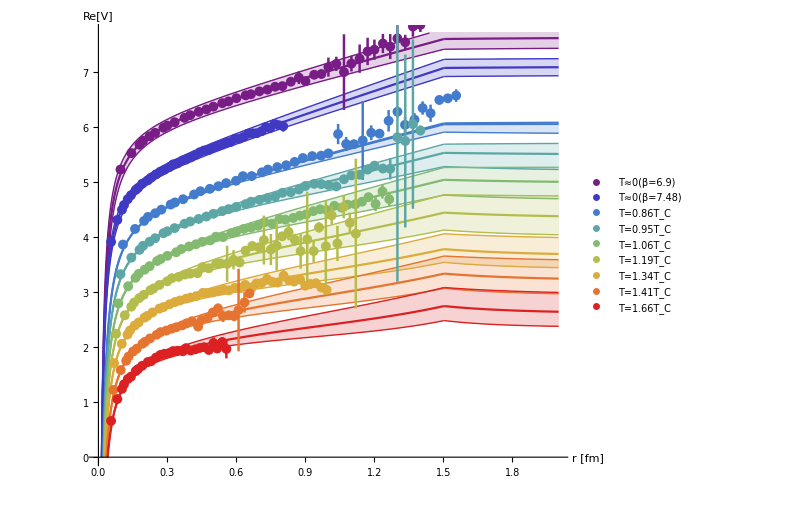

```mathematica
Show[{ReVanPlotError,ReVdatPlot}]
```

### Imag Part

```mathematica
Shift=1.
```

1.

```mathematica
For[l=1,l≤ 7,l++,PotImRescale[l]=ImVdataTe[l]/.{a_,b_,c_}:>{a-Shift*l+7*Shift,b,c}];
```

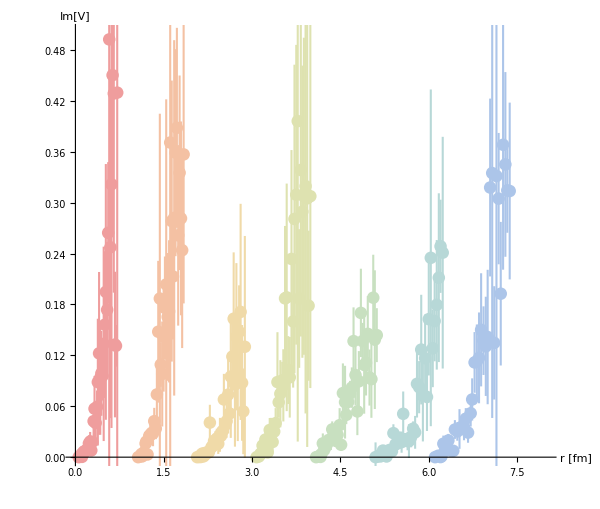

```mathematica
ImVdatPlot=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,1,7}],PlotRange->{{0,8},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

```mathematica
ImVe[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,1]=Block[{l=1,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[1,-1]=Block[{l=1,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,1/1000,αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,1]=Block[{l=2,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[2,-1]=Block[{l=2,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[3,1]=Block[{l=3,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[3,-1]=Block[{l=3,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[4,1]=Block[{l=4,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[4,-1]=Block[{l=4,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[5,1]=Block[{l=5,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[5,-1]=Block[{l=5,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[6,1]=Block[{l=6,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[6,-1]=Block[{l=6,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[7,1]=Block[{l=7,a=1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
ImVe[7,-1]=Block[{l=7,a=-1},ParallelTable[{r-Shift*l+7*Shift,ImVsI[r/0.197327,rsb,mdfitrandfinal[[l,1]]+a mdfitrandfinal[[l,2]],αcontβ1[[l+2]],σcontβ1[[l+2]],T[[l]]]},{r,1/1000,2,1/100}]];
```

```mathematica
TempP2={"T=0.86T_C","T=0.95T_C","T=1.06T_C","T=1.19T_C","T=1.34T_C","T=1.41T_C","T=1.66T_C"};
```

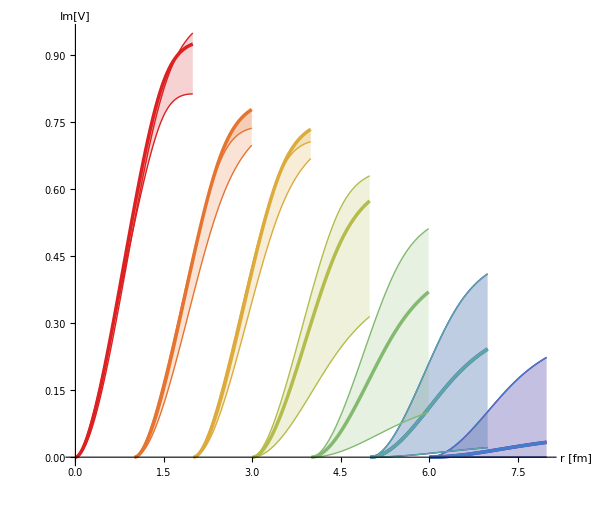

```mathematica
ImVanPlotError=ListPlot[{ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[1,0],ImVe[1,1],ImVe[1,-1],ImVe[2,0],ImVe[2,1],ImVe[2,-1],ImVe[3,0],ImVe[3,1],ImVe[3,-1],ImVe[4,0],ImVe[4,1],ImVe[4,-1],ImVe[5,0],ImVe[5,1],ImVe[5,-1],ImVe[6,0],ImVe[6,1],ImVe[6,-1],ImVe[7,0],ImVe[7,1],ImVe[7,-1]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.471412, 0.108766, 0.527016],Thin},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.250728, 0.225386, 0.769152],Thin},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.266122, 0.486664, 0.802529],Thin},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.36048, 0.655759, 0.645692],Thin},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.513417, 0.72992, 0.440682],Thin},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.705038, 0.742591, 0.299167],Thin},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.863512, 0.670771, 0.236564],Thin},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.902853, 0.453964, 0.192014],Thin},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],Thin},{RGBColor[0.857359, 0.131106, 0.132128],Thin}},Filling->Flatten[Table[{i->{i+1},i->{i+2}},{i,1,27,3}]],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

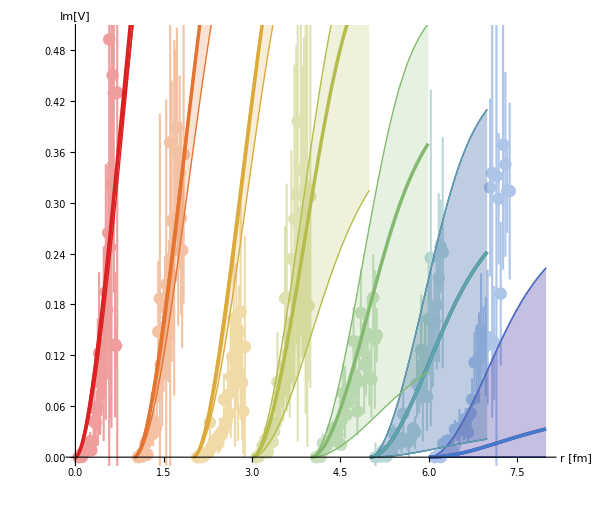

```mathematica
Show[ImVdatPlot,ImVanPlotError]
```